```mathematica
ClearAll["Global`*"]
```

```mathematica
kernel[t_,x_,a_]=Exp[-a^2(x-t)^2]
```

ⅇ^(-a^2 (-t+x)^2)

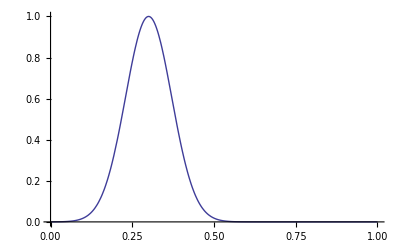

```mathematica
Plot[kernel[t,0.3,10],{t,0,1},PlotStyle ->Thick]
```

```mathematica
dtkernel[t_,x_,a_]=D[kernel[t,x,a],t]
```

2 a^2 ⅇ^(-a^2 (-t+x)^2) (-t+x)

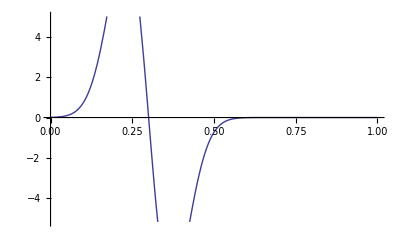

```mathematica
Plot[dtkernel[t,0.3,10],{t,0,1},PlotStyle ->Thick]
```

```mathematica
dtxkernel[t_,x_,a_]=Simplify[D[dtkernel[t,x,a],x]]
```

ⅇ^(-a^2 (t-x)^2) (2 a^2-4 a^4 (t-x)^2)

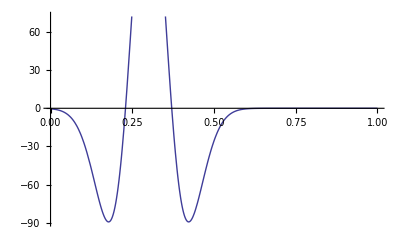

```mathematica
Plot[dtxkernel[t,0.3,10],{t,0,1},PlotStyle ->Thick]
```

```mathematica
ik[a_]=Integrate [kernel[t,t,a],{t,0,1}]
```

1

```mathematica
idtxk[a_]=Integrate [dtxkernel[t,t,a],{t,0,1}]
```

2 a^2

```mathematica
integkukv[u_,v_,a_]=Integrate[kernel[x,u,a]kernel[x,v,a],{x,0,1}]
```

(ⅇ^(-1/2 a^2 (u-v)^2) √(π/2) (-Erf[(a (-2+u+v))/(√2)]+Erf[(a (u+v))/(√2)]))/(2 a)

```mathematica
N[Simplify[integkukv[0,1,10]]]
```

2.41733×10^-23

```mathematica
N[Integrate[kernel[x,1/2,10]kernel[x,1/2,10],{x,0,1}]]
```

0.125331

```mathematica
integkukv[u_,v_,a_]=Simplify[Integrate[dtkernel[t,u,a]dtkernel[t,v,a],{t,0,1}]]
```

1/4 a (ⅇ^(-a^2 (2+u^2+u v+v^2-2 (u+v))) (2 a ⅇ^(a^2 u v) (-2+u+v)+ⅇ^(1/2 a^2 (u^2+(-2+v)^2+4 u (-1+v))) √(2 π) (-1+a^2 (u-v)^2) Erf[(a (-2+u+v))/(√2)])-ⅇ^(-a^2 (u^2+u v+v^2)) (2 a ⅇ^(a^2 u v) (u+v)+ⅇ^(1/2 a^2 (u^2+4 u v+v^2)) √(2 π) (-1+a^2 (u-v)^2) Erf[(a (u+v))/(√2)]))